# 紧聚焦仿真-MMA程序

Lawrence Lee

北京理工大学

2020.11.9

绘制了基模、H_01、H_10、径向偏振、角向偏振模式紧聚焦后的光场分布图，但由于采用ListDensityPlot函数绘图，故所绘制仍是标量图，需后面换成其他绘制矢量图的函数。
参考资料：Principles of Nano-Optics-3.6节【基模、H_01、H_10】，3.7节【径向偏振、角向偏振】

可能用到的程序包

<< MaTeX`;
<< Notation`;
<< MATLink`;
OpenMATLAB[];
<< GroupTheory`;
<< Quantum`Notation`;
SetQuantumAliases[];

自动计算的部分

```mathematica
<<MaTeX`
<<Notation`
Symbolize[Subscript[Δf, L]]
Symbolize[Subscript[Δf, T]]
Symbolize[Subscript[z, R]]
Symbolize[Subscript[w, 0]]
Symbolize[z̃]
Symbolize[Subscript[γ, 0]]
Symbolize[Subscript[Ε, 0]]
Symbolize[Subscript[x, ∞]]
Symbolize[Subscript[y, ∞]]
Symbolize[Subscript[z, ∞]]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[θ, max]]
Symbolize[OverVector[Subscript[Ε, ∞]]]
Symbolize[OverVector[Subscript[Ε, int]]]
Symbolize[OverVector[Subscript[n, ϕ]]]
Symbolize[OverVector[Subscript[n, ρ]]]
Symbolize[OverVector[Subscript[n, θ]]]
Symbolize[Subscript[ℓ, 1]]
Symbolize[Subscript[ℓ, 2]]
Symbolize[(e⃗)_R]
Symbolize[(e⃗)_L]
Symbolize[(e⃗)_x]
Symbolize[(e⃗)_y]
Symbolize[Subscript[β, 0]]
Symbolize[Subscript[ρ, s]]
```

```mathematica
<<Notation`
Symbolize[Subscript[I, 00]]
Symbolize[Subscript[I, 01]]
Symbolize[Subscript[I, 02]]
Symbolize[Subscript[I, 10]]
Symbolize[Subscript[I, 11]]
Symbolize[Subscript[I, 12]]
Symbolize[Subscript[I, 13]]
Symbolize[Subscript[I, 14]]
Symbolize[Subscript[f, ω]]
Symbolize[Subscript[θ, max]]
Symbolize[Subscript[f, 0]]
Symbolize[Subscript[ω, 0]]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[Ε, 0]]
Symbolize[Subscript[Ε, x]]
Symbolize[Subscript[Ε, y]]
Symbolize[Subscript[Ε, z]]
Symbolize[𝕀]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

## HankelTransformation

## 1. 基模

#### 1. 初始设置

```mathematica
Subscript[I, 00]==∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ(1+cosθ)e^ikzcosθ Subscript[J, 0](kρsinθ)dθ
==∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](kρsinθ)dθ+∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ cosθ e^ikzcosθ Subscript[J, 0](kρsinθ)dθ
==∫_0^Subscript[θ, max] (-cos(θ))(-Sec[θ])(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ)dθ+∫_0^Subscript[θ, max] -(cosθ)^(1/2)sinθ (-cosθ) e^ikzcosθ Subscript[J, 0](ρ ksinθ)dθ
==∫_0^Subscript[θ, max] Sec[θ] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ) cos(θ) dθ+∫_0^Subscript[θ, max] -(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ ksinθ)  cosθdθ
==∫_0^Subscript[θ, max] (Sec[θ])(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ)cos(θ)dθ+∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ ksinθ) cos(θ)dθ
==∫_0^Subscript[θ, max] (Sec[θ])(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ)cos(θ)dθ+∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ ksinθ) cos(θ)dθ
==∫_0^Subscript[θ, max] (Sec[θ])(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ)d Sin[θ]+∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ ksinθ) d Sin[θ]
==∫_0^Subscript[θ, max] (Sec[θ])(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ)d Sin[θ]+∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ ksinθ) d Sin[θ]
```

```mathematica
Expand[Cos[θ]]==Sin[π/2+θ]
```

True

Expand

```mathematica
==∫_0^Subscript[θ, max] sinθ  (cosθ)^(-1/2)e^ikzcosθ Subscript[J, 0](ρ k sinθ)d Sin[θ]+∫_0^Subscript[θ, max] sinθ  (cosθ)^(1/2) e^ikzcosθ Subscript[J, 0](ρ ksinθ) d Sin[θ]
```

则

```mathematica
√(1-Sin[θ]^2)
```

```mathematica
Subscript[f, 1]= (√(1-Sin[θ]^2))^(-1/2)e^(ikz √(1-Sin[θ]^2))
Subscript[f, 2]=(√(1-Sin[θ]^2))^(1/2) e^(ikz √(1-Sin[θ]^2))
令Sin[θ]=t
Subscript[f, 1]= (√(1-t^2))^(-1/2)e^(ik z √(1-t^2))
Subscript[f, 2]=(√(1-t^2))^(1/2) e^(ik z √(1-t^2))
```

则原式变为

```mathematica
==1/k^2∫_0^Sin[Subscript[θ, max]] k t   (√(1-1/k^2 k^2 t^2))^(-1/2)e^(i k z √(1-1/k^2 k^2 t^2))Subscript[J, 0](ρ k t)d k t+1/k^2∫_0^Sin[Subscript[θ, max]] k t  (√(1-1/k^2 k^2 t^2))^(1/2) e^(i k z √(1-1/k^2 k^2 t^2))Subscript[J, 0](ρ k t) d k t

==1/k^2∫_0^(k Sin[Subscript[θ, max]]) u   (√(1-1/k^2 u^2))^(-1/2)e^(i k z √(1-1/k^2 u^2))Subscript[J, 0](ρ u)d u+1/k^2∫_0^(k Sin[Subscript[θ, max]]) u  (√(1-1/k^2 u^2))^(1/2) e^(i k z √(1-1/k^2 u^2))Subscript[J, 0](ρ u) d u
```

```mathematica
k=.
z=.
u=.
ρ=.
(*HankelTransform[(√(1-1/k^2 u^2))^(-1/2)ⅇ^(ⅈ k z √(1-1/k^2 u^2)),u,ρ]*)
k=1
z=0
(√(1-u^2/k^2))^(-1/2)ⅇ^(ⅈ k z √(1-u^2/k^2))
(*HankelTransform[(√(1-u^2/k^2))^(-1/2)ⅇ^(ⅈ k z √(1-u^2/k^2)),u,ρ]*)
HankelTransform[1/((1-u^2)^(1/4)),u,ρ]
```

1

0

1/((1-u^2)^(1/4))

HankelTransform[1/((1-u^2)^(1/4)),u,ρ,0]

```mathematica
HankelTransform[1/((1-r^2)^(1/4)),r,s]
```

HankelTransform[1/((1-r^2)^(1/4)),r,s,0]

```mathematica
HankelTransform[(1-r^2)^(1/4),r,s]
```

HankelTransform[(1-r^2)^(1/4),r,s,0]

```mathematica
HankelTransform[Cos[θ],θ,s]
```

```mathematica
FittedModel
```

```mathematica
Subscript[f, 0]=Subscript[ω, 0]/(f*Sin[Subscript[θ, max]]);
Subscript[f, ω][θ_]:=ⅇ^(-(Sin[θ]/(Subscript[f, 0]*Sin[Subscript[θ, max]]))^2)
(*定义Subscript[I, ij]*)
Subscript[I, 00][ρ_]:=NIntegrate[((((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]) (1+Cos[θ])) BesselJ[0,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 01][ρ_]:=NIntegrate[(((Subscript[f, ω][θ] √Cos[θ]) (-Sin[θ])^2) BesselJ[1,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 02][ρ_]:=NIntegrate[((((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]) (1-Cos[θ])) BesselJ[2,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 10][ρ_]:=NIntegrate[(((Subscript[f, ω][θ] √Cos[θ]) (-Sin[θ])^3) BesselJ[0,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 11][ρ_]:=NIntegrate[((((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]^2) (1+3 Cos[θ])) BesselJ[1,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 12][ρ_]:=NIntegrate[((((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]^2) (1-Cos[θ])) BesselJ[1,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 13][ρ_]:=NIntegrate[(((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]^3) BesselJ[2,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 14][ρ_]:=NIntegrate[((((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]^2) (1-Cos[θ])) BesselJ[3,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[n, 1]=1.;
Subscript[n, 2]=1.518;
NA=1.3;
Subscript[θ, max]=Solve[NA==Subscript[n, 2]*Sin[Subscript[θ, max]],Subscript[θ, max],InverseFunctions->True]⟦1,1⟧/.Rule->Set;
Subscript[ω, 0]=0.532*100;(*束腰的100倍*)
f=0.16*1000;(*100倍物镜的焦距一般为0.13~0.19mm*)
k=2π;
Subscript[Ε, 0]=100;(*估计功率为100mW*)
```

#### 2. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f)/2)√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{Subscript[I, 00][ρ]+Subscript[I, 02][ρ]Cos[2φ]}, {Subscript[I, 02][ρ]Sin[2φ]}, {-2*ⅈ*Subscript[I, 01][ρ]Cos[φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 3. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,.0001,3,.01},{φ,0,2π,.01}];//AbsoluteTiming
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,.00000001,3,.01},{φ,0,2π,.01}];//AbsoluteTiming
```

{7921.07,Null}

{3968.15,Null}

```mathematica
data//Dimensions
Flatten[data,1]//Dimensions
```

{300,629,3}

{188700,3}

```mathematica
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
```

```mathematica
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 4. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 2. 模

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ*Subscript[I, 11][ρ]Cos[φ]+ⅈ*Subscript[I, 14][ρ]Cos[3φ]}, {-ⅈ*Subscript[I, 12][ρ]Sin[φ]+ⅈ*Subscript[I, 14][ρ]Sin[3φ]}, {-2*Subscript[I, 10][ρ]+2*Subscript[I, 13][ρ]*Cos[2φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.0001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 3. 模

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ(Subscript[I, 11][ρ]+2*Subscript[I, 12][ρ])Sin[φ]+ⅈ*Subscript[I, 14][ρ]Sin[3φ]}, {-ⅈ*Subscript[I, 12][ρ]Cos[φ]-ⅈ*Subscript[I, 14][ρ]Cos[3φ]}, {2*Subscript[I, 13][ρ]Sin[2φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.000000001,3,.01},{φ,0,2π,.001}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 4. 径向偏振

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ(Subscript[I, 11][ρ]-Subscript[I, 12][ρ])Cos[φ]}, {ⅈ(Subscript[I, 11][ρ]-Subscript[I, 12][ρ])Sin[φ]}, {-4*Subscript[I, 10][ρ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度和相位

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,8,.05},{φ,0,2π,.05}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 5. 角向偏振

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ(Subscript[I, 11][ρ]+3 Subscript[I, 12][ρ])Sin[φ]}, {-ⅈ(Subscript[I, 11][ρ]+3 Subscript[I, 12][ρ])Cos[φ]}, {0}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.000000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度和相位

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.00000001,0.3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 3. HLG为基模

### 1. 修改说明

加入了变量

为避免与紧聚焦公式中的混淆，将此处的改为

将初相位改为（变量）和（常量）

### 2. 代码

#### 1. 输入参数

固定参数

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*输入波长，单位um*)
λ=0.532;
```

可调参数

```mathematica
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*输入固有横模指数n*)
n=15.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=30.;
(*输入固有纵模指数l*)
l=1.;
(*输入庞加莱球上的坐标(α,β)*)
α=π/2;
β=π/2;
(*输入初相位*)
γ=π/2;
(*输入相干叠加次数M*)
M=4.;
(*输入坐标范围a*)
a=3;
(*绘制2D图*)
z=0;
```

计算腔径，需首先清楚R的赋值

```mathematica
(*-Graphics-,令-Graphics-计算-Graphics-*)
R=.
L=1.;
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
```

#### 2. 定义函数

```mathematica
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
Notation[Subscript[d, n_,m_]^k_[β_] ⟺ WignerD[{(n_+m_)/2,k_-(n_+m_)/2,(n_-m_)/2},β_]]
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_,z_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/w[z_] Subscript[H, n_][(√2 x_)/w[z_]]Subscript[H, m_][(√2 y_)/w[z_]]Exp[-(x_^2+y_^2)/(w[z_])^2]]
Notation[Subscript[ψ, n_,m_,l_]^(HG)[x_,y_,z_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_,z_]Exp[ⅈ*Subscript[k, n_,m_,l_]*z̃[x_,y_,z_]-ⅈ(m_+n_+1)ϑ[z_]]]
Notation[Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_] ⟺ Exp[ⅈ(n_+m_)/2 α_]∑_(k=0)^(n_+m_) Exp[ⅈ*k*α_]*Subscript[d, n_,m_]^k[β_]Subscript[ψ, k,n_+m_-k,l_]^(HG)[x_,y_,z_]]
Notation[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ 1/2^(M_/2)∑_(K=0)^M_ √Binomial[M_,K] Exp[ⅈ*K*γ_]*Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Arg[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]*(Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_])*//Norm]
```

#### 3. 绘图

```mathematica
DensityPlot[#,{x,-a,a},{y,-a,a},PlotRange->All,Exclusions->None,Background->White,ColorFunction->GrayLevel,PlotPoints->150,ImageSize->{750,750},PlotLegends->#2,PlotLabel->#3,Frame->True,FrameLabel->#4]&@@@{{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,α,β,γ,M],,-Graphics-,-Graphics-},{(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,α,β,γ,M],,-Graphics-,-Graphics-}}//Column//CloudDeploy

SystemOpen[%]
```

CloudObject[https://www.wolframcloud.com/obj/737cac44-4430-4b9a-b576-93a91db93e87]

## 1. SU(2)模

```mathematica
Subscript[n, 1]=1.;
Subscript[n, 2]=1.518;
NA=1.3;
Subscript[θ, max]=.
Subscript[θ, max]=Solve[NA==Subscript[n, 2]*Sin[Subscript[θ, max]],Subscript[θ, max],InverseFunctions->True]⟦1,1⟧/.Rule->Set;

f=0.481;(*100倍物镜的焦距一般为0.13~0.19mm*)
k=(2π)/λ;
Notation[Subscript[f, 0] ⟺ Subscript[w, 0]/(f Sin[Subscript[θ, max]])]
 Subscript[Ε, 0]=100;
Subscript[f, 0]
```

0.998997

```mathematica
Notation[Ψ_(-Graphics-)^(SU(2))[θ_,ϕ_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Sin[θ_]Cos[ϕ_],f Sin[θ_]Sin[ϕ_],0,α,β,γ,M]//N]
```

```mathematica
(Ψ_(-Graphics-)^(SU(2)))[Subscript[θ, max],0]
```

-0.0420336+0.0402489 ⅈ

```mathematica
Notation[Ψ_(-Graphics-)^(SU(2))[θ_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Sin[θ_]Cos[0],f Sin[θ_]Sin[0],0,α,β,γ,M]//N]
```

```mathematica
(Ψ_(-Graphics-)^(SU(2)))[Subscript[θ, max]]
```

-0.0420336+0.0402489 ⅈ

#### 1. 初始设置

```mathematica
(*定义Subscript[I, ij]*)
Subscript[I, 00][ρ_]:=NIntegrate[(((((Ψ_(-Graphics-)^(SU(2)))[θ] √Cos[θ]) Sin[θ]) (1+Cos[θ])) BesselJ[0,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 01][ρ_]:=NIntegrate[((((Ψ_(-Graphics-)^(SU(2)))[θ] √Cos[θ]) (-Sin[θ])^2) BesselJ[1,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 02][ρ_]:=NIntegrate[(((((Ψ_(-Graphics-)^(SU(2)))[θ] √Cos[θ]) Sin[θ]) (1-Cos[θ])) BesselJ[2,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
```

```mathematica
Subscript[I, 00][1]
Subscript[I, 01][1]
Subscript[I, 02][1]
```

0.000993794-0.000973806 ⅈ

0.000874985-0.00084987 ⅈ

-0.0000432257+0.0000433869 ⅈ

#### 2. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f)/2)√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{Subscript[I, 00][ρ]+Subscript[I, 02][ρ]Cos[2φ]}, {Subscript[I, 02][ρ]Sin[2φ]}, {-2*ⅈ*Subscript[I, 01][ρ]Cos[φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

```mathematica
Ε[1,1]
```

{{-0.106005-0.137698 ⅈ},{0.00423008+0.00536262 ⅈ},{-0.128554+0.0980236 ⅈ}}

#### 3. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,.0001,3,1},{φ,0,2π,1}];//AbsoluteTiming
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,.00000001,3,1},{φ,0,2π,1}];//AbsoluteTiming
```

$Aborted

LinkObject::linkd: Unable to communicate with closed link LinkObject["A:\Program Files\Wolfram Research\Mathematica\12.1\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,2685,11].

KernelObject::rdead: Subkernel connected through … appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {46} assigned to ….

LaunchKernels::clone: Kernel … resurrected as ….

```mathematica
data//Dimensions
Flatten[data,1]//Dimensions
```

{300,629,3}

{188700,3}

```mathematica
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
```

```mathematica
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 4. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 2

```mathematica
Notation[Ψ_(-Graphics-)^(SU(2))[θ_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Sin[θ_]Cos[0],f Sin[θ_]Sin[0],0,α,β,γ,M]//N]
```

```mathematica
(Ψ_(-Graphics-)^(SU(2)))[Subscript[θ, max]]
```

-0.0420336+0.0402489 ⅈ

```mathematica
HankelTransform
```

按照Focusing of high numerical aperture cylindricalvector beams的方法算径向偏振

```mathematica
<<Notation`
```

```mathematica
(*Notation[Ψ^(SU(2))[ρ_] ⟺ NIntegrate[√Cos[θ] Sin[2θ]Ψ_(-Graphics-)^(SU(2))[θ]BesselJ[1,(k ρ_) Sin[θ]],{θ,0,Subscript[θ, max]}]]
Notation[𝒫^(SU(2))[ρ_] ⟺ Arg[Ψ^(SU(2))[ρ_]]//Norm]
Notation[𝕀^(SU(2))[ρ_] ⟺ Ψ^(SU(2))[ρ_]*(Ψ^(SU(2))[ρ_])*//Norm]*)
```

```mathematica
Ψ[ρ_]:=NIntegrate[√Cos[θ] Sin[2θ](Ψ_(-Graphics-)^(SU(2)))[θ]BesselJ[1,(k ρ) Sin[θ]],{θ,0,Subscript[θ, max]}]
𝒫[ρ_]:=Arg[Ψ[ρ]]//Norm
𝕀[ρ_]:=Ψ[ρ]*(Ψ[ρ])*//Norm
```

```mathematica
Ψ[1]
𝒫[1]
𝕀[1]
```

-0.000643742+0.000630456 ⅈ

2.36662

8.11878×10^-7

```mathematica
a
```

3

```mathematica
DensityPlot[#,{x,-a,a},{y,-a,a},PlotRange->All,Exclusions->None,Background->White,ColorFunction->GrayLevel,ImageSize->{750,750},Frame->True]&@@@{{𝒫[√(x^2+y^2)]},{𝕀[√(x^2+y^2)]}}//Column//CloudDeploy

SystemOpen[%]
```

NIntegrate::inumr: The integrand 0.25 BesselJ[1,11.8105 √(x^2+y^2) Sin[θ]] √Cos[θ] («1») Sin[2 θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.02824}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

SystemOpen[$Aborted]

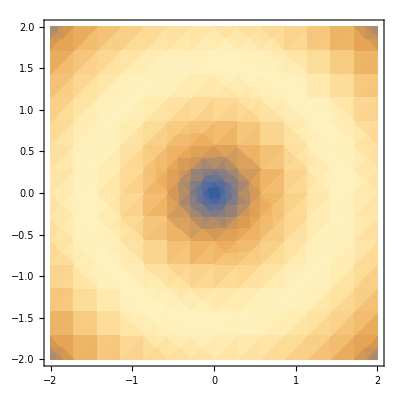

```mathematica
DensityPlot[Sin[√(x^2+y^2)],{x,-2,2},{y,-2,2}]
```

```mathematica
DensityPlot[Sin[√(x^2+y^2)],{x,-2,2},{y,-2,2}]
```